# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];*)
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}
```

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

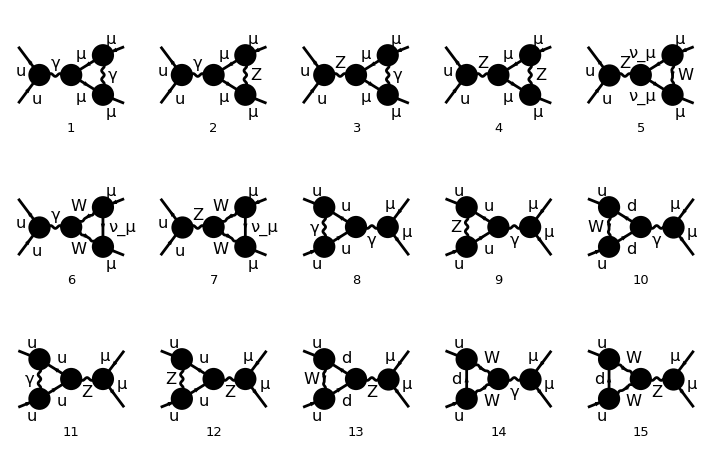

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

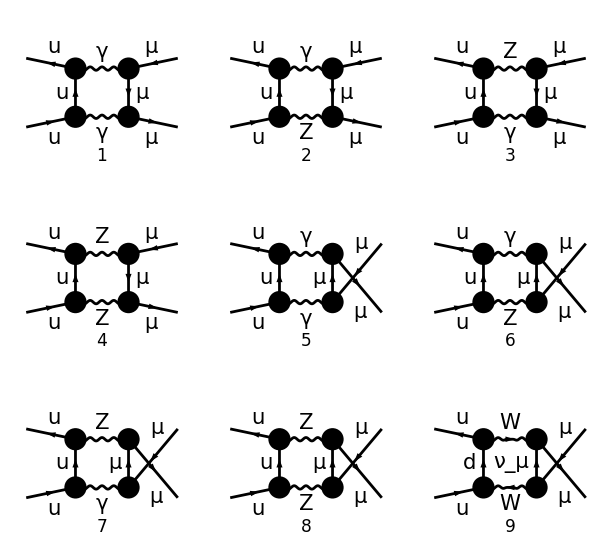

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

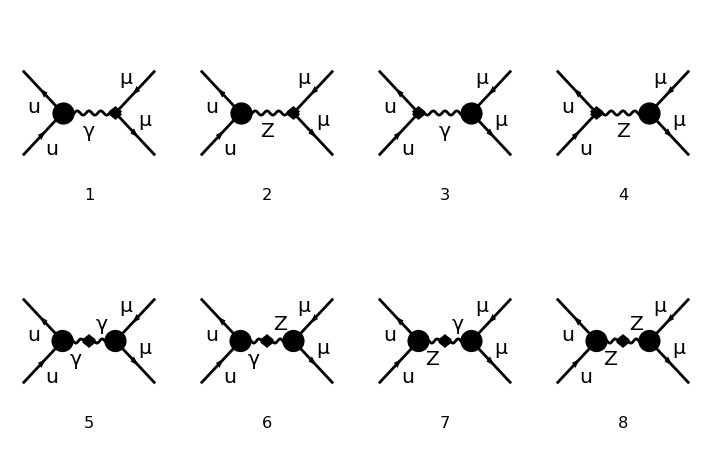

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
tboxzz=totbbox[4][[1]]//.MASSES;
uboxzz=totbbox[4][[2]]//.MASSES;
wwbox=totbbox[5]//.MASSES;
```

```mathematica
(*funzione per semplificare propagatori*)
numer[x__ PropagatorDenominator[p_,MZ] PropagatorDenominator[p_,mzg]]:=numer[x/(MZ^2-mzg^2)(PropagatorDenominator[p,MZ]-PropagatorDenominator[p,mzg])];
numerw[x__ PropagatorDenominator[p_,MW] PropagatorDenominator[p_,mwg]]:=numerw[x/(MW^2-mwg^2)(PropagatorDenominator[p,MW]-PropagatorDenominator[p,mwg])];
```

```mathematica
(*BORN*)
born=Part[born1,{2}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES;
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}] 
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].((ⅈ EL (I3U-QZUl SW2) ga[Lorbn1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lorbn1].om_+)/CW).u[p1,0]],CONJ[ū[k1,0].((ⅈ EL (I3L-QZLl SW2) ga[Lorbn2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lorbn2].om_+)/CW).v[k2,0]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

((SP[k1,Lorbn1]+SP[k2,Lorbn1]) (SP[k1,Lorbn2]+SP[k2,Lorbn2]))/(MZ2 (-MZ2 ZGAUGE+(k1+k2)^2))+((SP[-(k1),Lorbn1]+SP[-(k2),Lorbn1]) (SP[k1,Lorbn2]+SP[k2,Lorbn2])+MZ2 SP[Lorbn1,Lorbn2])/(MZ2 (-MZ2+(k1+k2)^2))

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Semplificazione propagatori

Divisione in termini dipendenti da gauge e indipendenti

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
(*box w*)
wnumerat=DeleteCases[wwbox, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
```

1/(16 π^4)ⅈ 1/(q1)^2 1/(-MZ2+(p2+q1)^2) (g[Lor3,Lor4]+((-(p2)-q1)[Lor3]+ZGAUGE (p2+q1)[Lor3]) (p2+q1)[Lor4] 1/(-MZ2 ZGAUGE+(p2+q1)^2)) 1/(p2+q1-k2)^2 1/(-MZ2+(p2+q1-k1-k2)^2) (g[Lor1,Lor2]+((p2+q1-k1-k2)[Lor1]+ZGAUGE (-(p2)-q1+k1+k2)[Lor1]) (-(p2)-q1+k1+k2)[Lor2] 1/(-MZ2 ZGAUGE+(p2+q1-k1-k2)^2))

1/(16 π^4)ⅈ 1/(q1)^2 1/(-MZ2+(p2+q1)^2) (g[Lor3,Lor4]+((-(p2)-q1)[Lor3]+ZGAUGE (p2+q1)[Lor3]) (p2+q1)[Lor4] 1/(-MZ2 ZGAUGE+(p2+q1)^2)) 1/(p2+q1-k1)^2 1/(-MZ2+(p2+q1-k1-k2)^2) (g[Lor1,Lor2]+((p2+q1-k1-k2)[Lor1]+ZGAUGE (-(p2)-q1+k1+k2)[Lor1]) (-(p2)-q1+k1+k2)[Lor2] 1/(-MZ2 ZGAUGE+(p2+q1-k1-k2)^2))

1/(16 π^4)ⅈ 1/(q1)^2 1/(-MW2+(p2+q1)^2) (g[Lor3,Lor4]+((-(p2)-q1)[Lor3]+WGAUGE (p2+q1)[Lor3]) (p2+q1)[Lor4] 1/(-MW2 WGAUGE+(p2+q1)^2)) 1/(p2+q1-k1)^2 1/(-MW2+(p2+q1-k1-k2)^2) (g[Lor1,Lor2]+((p2+q1-k1-k2)[Lor1]+WGAUGE (-(p2)-q1+k1+k2)[Lor1]) (-(p2)-q1+k1+k2)[Lor2] 1/(-MW2 WGAUGE+(p2+q1-k1-k2)^2))

```mathematica
(*prove semplificaz propagatore generico*)
sempp[propag_]:=Module[{t1,t11,t111,t1111,t2,t22,t222,t2222,tnumerat1,tnumerat2,t1w,t11w,t111w,t1111w,t2w,t22w,t222w,t2222w,tnumerat1w,tnumerat2w},
propagatore=propag;
tnn=Select[propagatore,MemberQ[#,ZGAUGE|MZ,Infinity]&];(*seleziona i termini contenenti ZGAUGE oppure massa MZ*)
tnn2=Select[propagatore,FreeQ[#,ZGAUGE|MZ,Infinity]&];(*seleziona i termini restanti, passaggio intermedio*)
	tnnw=Select[tnn2,MemberQ[#,WGAUGE|MW,Infinity]&];(*seleziona i termini contenenti WGAUGE oppure massa MW in tnn2*)
	tnnrest=Select[tnn2,FreeQ[#,WGAUGE|MW,Infinity]&];(*seleziona i termini restanti*)
(*propagatore=tnn*tnnw*tnnrest*)

(*ZGAUGE*)
Which[Length[tnn]===2,(*caso di diagrammi con γ e Z*)
	t1=tnn//Expand;
	t11=numer/@t1/.numer->Sequence//Simplify;
	t111=Collect[t11,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
	t1111=Collect[t111,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
	tnumerat1=t1111//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
	totnum=tnumerat1,

	Length[tnn]>2,(*caso con 2 Z*)
		t1=tnn[[1;;Length[tnn]/2]]//Expand;
		t11=numer/@t1/.numer->Sequence//Simplify;
		t111=Collect[t11,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111=Collect[t111,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat1=t1111//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]]->FourVector[a + b, Index[w]];

		t2=tnn[[Length[tnn]/2+1;;Length[tnn]]]//Expand;
		t22=numer/@t2/.numer->Sequence//Simplify;
		t222=Collect[t22,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t2222=Collect[t222,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat2=t2222//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]]->FourVector[a + b, Index[w]];
		totnum=tnumerat1*tnumerat2,

	True,
		totnum=1];

(*WGAUGE*)
Which[Length[tnnw]===2,(*caso di diagrammi con un solo W*)
		t1w=tnnw//Expand;
		t11w=numerw/@t1w/.numerw->Sequence//Simplify;
		t111w=Collect[t11w,PropagatorDenominator[x_,mwg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111w=Collect[t111w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat1w=t1111w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
		totnum1=tnumerat1w,

	Length[tnnw]>2,(*caso con 2 W*)
		t1w=tnnw[[1;;Length[tnnw]/2]]//Expand;
		t11w=numerw/@t1w/.numerw->Sequence//Simplify;
		t111w=Collect[t11w,PropagatorDenominator[x_,mwg],FullSimplify]//.WGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111w=Collect[t111w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->WGAUGE-1;
		tnumerat1w=t1111w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];

	t2w=tnnw[[Length[tnnw]/2+1;;Length[tnnw]]]//Expand;
	t22w=numerw/@t2w/.numerw->Sequence//Simplify;
	t222w=Collect[t22w,PropagatorDenominator[x_,mwg],FullSimplify]//.WGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
	t2222w=Collect[t222w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->WGAUGE-1;
	tnumerat2w=t2222w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
	totnum1=tnumerat1w*tnumerat2w,

	True,
		totnum1=1];


propagtot=totnum*totnum1*tnnrest];
```

```mathematica
tpropag=sempp[tnumerat]
upropag=sempp[unumerat]
wpropag=sempp[wnumerat]
```

1/(16 MZ2^2 π^4)ⅈ 1/(q1)^2 ((-(p2)-q1)[Lor3] (p2+q1)[Lor4] 1/(-MZ2+(p2+q1)^2)+MZ2 g[Lor3,Lor4] 1/(-MZ2+(p2+q1)^2)+(p2+q1)[Lor3] (p2+q1)[Lor4] 1/(-MZ2 ZGAUGE+(p2+q1)^2)) 1/(p2+q1-k2)^2 ((p2+q1-k1-k2)[Lor1] (-(p2)-q1+k1+k2)[Lor2] 1/(-MZ2+(p2+q1-k1-k2)^2)+MZ2 g[Lor1,Lor2] 1/(-MZ2+(p2+q1-k1-k2)^2)+(-(p2)-q1+k1+k2)[Lor1] (-(p2)-q1+k1+k2)[Lor2] 1/(-MZ2 ZGAUGE+(p2+q1-k1-k2)^2))

1/(16 MZ2^2 π^4)ⅈ 1/(q1)^2 ((-(p2)-q1)[Lor3] (p2+q1)[Lor4] 1/(-MZ2+(p2+q1)^2)+MZ2 g[Lor3,Lor4] 1/(-MZ2+(p2+q1)^2)+(p2+q1)[Lor3] (p2+q1)[Lor4] 1/(-MZ2 ZGAUGE+(p2+q1)^2)) 1/(p2+q1-k1)^2 ((p2+q1-k1-k2)[Lor1] (-(p2)-q1+k1+k2)[Lor2] 1/(-MZ2+(p2+q1-k1-k2)^2)+MZ2 g[Lor1,Lor2] 1/(-MZ2+(p2+q1-k1-k2)^2)+(-(p2)-q1+k1+k2)[Lor1] (-(p2)-q1+k1+k2)[Lor2] 1/(-MZ2 ZGAUGE+(p2+q1-k1-k2)^2))

1/(16 MW2^2 π^4)ⅈ 1/(q1)^2 ((-(p2)-q1)[Lor3] (p2+q1)[Lor4] 1/(-MW2+(p2+q1)^2)+MW2 g[Lor3,Lor4] 1/(-MW2+(p2+q1)^2)+(p2+q1)[Lor3] (p2+q1)[Lor4] 1/(-MW2 WGAUGE+(p2+q1)^2)) 1/(p2+q1-k1)^2 ((p2+q1-k1-k2)[Lor1] (-(p2)-q1+k1+k2)[Lor2] 1/(-MW2+(p2+q1-k1-k2)^2)+MW2 g[Lor1,Lor2] 1/(-MW2+(p2+q1-k1-k2)^2)+(-(p2)-q1+k1+k2)[Lor1] (-(p2)-q1+k1+k2)[Lor2] 1/(-MW2 WGAUGE+(p2+q1-k1-k2)^2))

```mathematica
(*propagatore born*)
bornpropag2
(*propagatore box, parte in comune fra t e u. propagatore box W*)
propagatT=tnumerat[[6]];
propagatU=unumerat[[6]];

ptot=DeleteCases[tpropag,propagatT,Infinity]+DeleteCases[upropag,propagatU,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
ptotw=DeleteCases[wpropag,propagatU,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

((SP[k1,Lorbn1]+SP[k2,Lorbn1]) (SP[k1,Lorbn2]+SP[k2,Lorbn2]))/(MZ2 (-MZ2 ZGAUGE+(k1+k2)^2))+((SP[-(k1),Lorbn1]+SP[-(k2),Lorbn1]) (SP[k1,Lorbn2]+SP[k2,Lorbn2])+MZ2 SP[Lorbn1,Lorbn2])/(MZ2 (-MZ2+(k1+k2)^2))

1/(8 MZ2^2 π^4 (q1)^2)ⅈ (((SP[p2,Lor1]+SP[q1,Lor1]+SP[-(k1),Lor1]+SP[-(k2),Lor1]) (SP[-(p2),Lor2]+SP[-(q1),Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MZ2+(p2+q1-k1-k2)^2)+((SP[-(p2),Lor1]+SP[-(q1),Lor1]+SP[k1,Lor1]+SP[k2,Lor1]) (SP[-(p2),Lor2]+SP[-(q1),Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MZ2 ZGAUGE+(p2+q1-k1-k2)^2)+(MZ2 SP[Lor1,Lor2])/(-MZ2+(p2+q1-k1-k2)^2)) (((SP[-(p2),Lor3]+SP[-(q1),Lor3]) (SP[p2,Lor4]+SP[q1,Lor4]))/(-MZ2+(p2+q1)^2)+((SP[p2,Lor3]+SP[q1,Lor3]) (SP[p2,Lor4]+SP[q1,Lor4]))/(-MZ2 ZGAUGE+(p2+q1)^2)+(MZ2 SP[Lor3,Lor4])/(-MZ2+(p2+q1)^2))

1/(16 MW2^2 π^4 (q1)^2)ⅈ (((SP[p2,Lor1]+SP[q1,Lor1]+SP[-(k1),Lor1]+SP[-(k2),Lor1]) (SP[-(p2),Lor2]+SP[-(q1),Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MW2+(p2+q1-k1-k2)^2)+((SP[-(p2),Lor1]+SP[-(q1),Lor1]+SP[k1,Lor1]+SP[k2,Lor1]) (SP[-(p2),Lor2]+SP[-(q1),Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MW2 WGAUGE+(p2+q1-k1-k2)^2)+(MW2 SP[Lor1,Lor2])/(-MW2+(p2+q1-k1-k2)^2)) (((SP[-(p2),Lor3]+SP[-(q1),Lor3]) (SP[p2,Lor4]+SP[q1,Lor4]))/(-MW2+(p2+q1)^2)+((SP[p2,Lor3]+SP[q1,Lor3]) (SP[p2,Lor4]+SP[q1,Lor4]))/(-MW2 WGAUGE+(p2+q1)^2)+(MW2 SP[Lor3,Lor4])/(-MW2+(p2+q1)^2))

```mathematica
denomt=tnumerat[[6]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
denomu=unumerat[[6]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

1/(p2+q1-k2)^2

1/(p2+q1-k1)^2

#### Trace

```mathematica
trg[s___,MM,u___]:=MM trg[s,u];
trg[z___,-G5]:=-trg[z,G5];
trg[a_,b_,G5]:=0;
trg[a_,b_,c_,d_,G5]:=-4 I LC myEps[a,b,c,d];
trg[x___,G5,G5,y___]:=trg[x,y];
trg[x__,G5]:=0/;OddQ[Length[{x}]];
trg[q___,G5,y__]:=trg[q,y,G5](-1)^(Length[{y}]);
trg[a_,b_]:=4 SP[a,b];
trg[w__]:=0/;OddQ[Length[{w}]] && FreeQ[{w},G5];

(*TRACE*)
trg[x__]:=Module[{temp,temp1,temp2,i,temp3},

temp={x};
temp1=Delete[temp,1];
temp2=Table[Delete[temp1,i],{i,1,Length[temp1]}];
temp3=Sum[SP[temp[[1]],temp1[[i]]](-1)^(i+1)*Apply[trg,temp2[[i]]],{i,1,Length[temp2]}];
temp3=Expand[temp3];

temp3
];
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:MM,b___]:=move2[a,dm,ChiralityProjector[pm],b];
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;
(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
(*calcolo traccia*)
trace2[chargesi_,statoi_,chargesf_,statof_]:=Module[{tr1i,tr2i,tr3i,tr1f,tr2f,tr3f,tracciai,tracciaf,chii,chff,tracei,tracef},

(*trace:*)
traceff[x___, DiracSpinor[z_,w_], DiracSpinor[z_,w_],y___]:=traceff[x,(DiracSlash[z]+w),y];(* ...u(p)u_bar(p) ... -> ...p_slash... *)(*sost. stato intermedio*)
traceff[ DiracSpinor[z_,w_],x__,DiracSpinor[z_,w_]]:=traceff[(DiracSlash[z]+w),x];(* v_bar(p)...v(p) ->p_slash... *)(*sost. stato esterno*)

(*stato i*)
tr1i=Table[traceff[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff->move2;(*sposto proiettori in fondo*)
chii=Delete[chargesi,Position[tr1i,0,{1}]];(*cariche*)
tr2i=Map[Distribute,1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
tr3i=DeleteCases[tr2i,1,{4}]//.move2->trg/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;(*espando e calcolo traccia*)
tracciai=tr3i/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]}//Expand;

(*stato f*)
tr1f=Table[traceff[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[Distribute[tr1f[[i]]],{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]//.traceff->move2;
If[FreeQ[statf,MM,Infinity],
chff=Delete[chargesf,Position[tr1f,0,{1}]],
chff=chargesf];(*cariche*)
tr2f=Map[Distribute,1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},{2}];
tr3f=DeleteCases[tr2f,1,{4}]//.move2->trg/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;
tracciaf=DeleteCases[tr3f/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]},0]//Expand;

Print["stato i ",1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},"\n stato f ",
1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

tracei=Thread[List[chii,tracciai]];
tracef=Thread[List[chff,tracciaf]];

Return[{tracei,tracef}]

];
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[-P1,_],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[-K1,_],Infinity]&],1];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[-P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1]//.move2->List;
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

prova1=trace2[chi,stati,chf,statf];

Return[{tr,prova1}](*closed fermion loop, trace*)
];
```

```mathematica
boxt=fermiontrace[tboxzz];
boxu=fermiontrace[uboxzz];
```

stato i {1/2 move2[gs[-(p1)],ga[Lor1],gs[-(q1)],ga[Lor3],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[-(p1)],ga[Lor1],gs[-(q1)],ga[Lor3],gs[p2],ga[Lorbn1],1+G5]}
 stato f {1/2 move2[gs[k2],ga[Lor4],gs[-(p2)-q1+k2],ga[Lor2],gs[-(k1)],ga[Lorbn2],1-G5],1/2 move2[gs[k2],ga[Lor4],gs[-(p2)-q1+k2],ga[Lor2],gs[-(k1)],ga[Lorbn2],1+G5]}

stato i {1/2 move2[gs[-(p1)],ga[Lor1],gs[-(q1)],ga[Lor3],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[-(p1)],ga[Lor1],gs[-(q1)],ga[Lor3],gs[p2],ga[Lorbn1],1+G5]}
 stato f {1/2 move2[gs[k2],ga[Lor2],gs[p2+q1-k1],ga[Lor4],gs[-(k1)],ga[Lorbn2],1-G5],1/2 move2[gs[k2],ga[Lor2],gs[p2+q1-k1],ga[Lor4],gs[-(k1)],ga[Lorbn2],1+G5]}

```mathematica
(*suddivido lo stato i ed f (che hanno due termini ciascuno) in parte delle cariche e parte con myEps/senza myEps*)
```

```mathematica
Table[{chargeI[i]=boxt[[2,1,i,1]],
ieps[i]={Select[boxt[[2,1,i,2]],MemberQ[#,_myEps,Infinity]&]},
ineps[i]={Select[boxt[[2,1,i,2]],FreeQ[#,_myEps,Infinity]&]}}
,{i,1,Length[boxt[[2,1]]]}];
Table[{chargeF[i]=boxt[[2,2,i,1]],
feps[i]={Select[boxt[[2,2,i,2]],MemberQ[#,_myEps,Infinity]&]},
fneps[i]={Select[boxt[[2,2,i,2]],FreeQ[#,_myEps,Infinity]&]}}
,{i,1,Length[boxt[[2,2]]]}];
```

```mathematica
Table[{chargeIu[i]=boxu[[2,1,i,1]],
iepsu[i]={Select[boxu[[2,1,i,2]],MemberQ[#,_myEps,Infinity]&]},
inepsu[i]={Select[boxu[[2,1,i,2]],FreeQ[#,_myEps,Infinity]&]}}
,{i,1,Length[boxu[[2,1]]]}];
Table[{chargeFu[i]=boxu[[2,2,i,1]],
fepsu[i]={Select[boxu[[2,2,i,2]],MemberQ[#,_myEps,Infinity]&]},
fnepsu[i]={Select[boxu[[2,2,i,2]],FreeQ[#,_myEps,Infinity]&]}}
,{i,1,Length[boxu[[2,2]]]}];
```

```mathematica
(*Il fatto che però ci siano solo 3 impulsi indipendenti (per la conserv. p1+p2=k1+k2) rende i termini con myEps nulli perché non ci sono abbastanza quantità per saturare gli indici mantenendo l’antisimmetria.
quindi i prodotti sono solo fra termini con myEps e senza myEps ma non misti.*)
(*ho stato i con due termini (Q1i*i1,Q2i*i2) e stato f (Q1f*f1,Q2f*f2) a loro volta composti da parte con myEps e senza. faccio il prodotto. ho 4 termini STAT: STAT[1,1] STAT[1,2] STAT[2,1] STAT[2,2] *)
```

```mathematica
Table[{CHARGE[i,j]={chargeI[i]chargeF[j]},STAT[i,j]={ParallelMap[ieps[i]*#&,feps[j]]//Expand,ParallelMap[ineps[i]*#&,fneps[j]]}//.List->Plus//Expand},{i,1,2},{j,1,2}]
```

{{{{-(64 Alfa Alfa2 π^3 (I3L-QZLl SW2)^3 (I3U-QZUl SW2)^3)/(CW2^3 SW2^3)},4 LC^2 SP[p1,Lorbn1] SP[p2,Lor3] SP[p2,Lorbn2] SP[q1,Lor4] SP[k1,Lor1] SP[k2,Lor2]-4 LC^2 SP[p1,Lor3] SP[p2,Lorbn1] SP[p2,Lorbn2] SP[q1,Lor4] SP[k1,Lor1] SP[k2,Lor2]+3503+4 LC^2 SP[p1,q1] SP[p2,k1] SP[k2,k2] SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,p2] SP[q1,k1] SP[k2,k2] SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2]},{{(64 Alfa Alfa2 π^3 QZLr^3 (I3U-QZUl SW2)^3)/CW2^3},-4 LC^2 SP[p1,Lorbn1] SP[p2,1] SP[1] SP[q1,Lor4] SP[k1,Lor1] SP[k2,Lor2]+3507}},{{1},1}}
 |  |  |  |

```mathematica
Table[{CHARGEu[i,j]={chargeIu[i]chargeFu[j]},STATu[i,j]={ParallelMap[iepsu[i]*#&,fepsu[j]]//Expand,ParallelMap[inepsu[i]*#&,fnepsu[j]]}//.List->Plus//Expand},{i,1,2},{j,1,2}]
```

{{{{-(64 Alfa Alfa2 π^3 (I3L-QZLl SW2)^3 (I3U-QZUl SW2)^3)/(CW2^3 SW2^3)},4 LC^2 SP[p1,Lorbn1] SP[p2,Lor3] SP[p2,Lorbn2] SP[q1,Lor4] SP[k1,Lor1] SP[k2,Lor2]-4 LC^2 SP[p1,Lor3] SP[p2,Lorbn1] SP[p2,Lorbn2] SP[q1,Lor4] SP[k1,Lor1] SP[k2,Lor2]+2605+4 LC^2 SP[p1,q1] SP[p2,q1] SP[k1,k2] SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,p2] SP[q1,q1] SP[k1,k2] SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2]},{{(64 Alfa Alfa2 π^3 QZLr^3 (I3U-QZUl SW2)^3)/CW2^3},-4 LC^2 SP[p1,Lorbn1] SP[p2,1] SP[1] SP[q1,Lor4] SP[k1,Lor1] SP[k2,Lor2]+2609}},{{1},1}}
 |  |  |  |

### Semplificazioni/sostituzioni

```mathematica
(*per verificare invarianza di gauge (data dalla somma del contributo T e U) moltiplico gli stati i/f della traccia per i fattori di ptot e bornpropag2 contenenti GAUGE e uso funzione sempl2 per semplificare i termini->la somma deve dare zero.*)
```

```mathematica
(*regole di sostituzione dei denominatori e regole inverse*)
SOST={-MZ2+(P2+Q1)^2->DMZQ1P2,-MZ2 ZGAUGE+(P2+Q1)^2->DMZGQ1P2,
-MW2+(P2+Q1)^2->DMWQ1P2,-MW2 WGAUGE+(P2+Q1)^2->DMWGQ1P2,
-MZ2+(K1+K2)^2->DMZK1K2,-MZ2 ZGAUGE+(K1+K2)^2->DMZGK1K2,
-MZ2+(P2+Q1-K1-K2)^2->DMZQ1P2K1K2,-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2->DMZGQ1P2K1K2,
-MW2+(P2+Q1-K1-K2)^2->DMWQ1P2K1K2,-MW2 WGAUGE+(P2+Q1-K1-K2)^2->DMWGQ1P2K1K2,
MZ2-(K1+K2)^2->-DMZK1K2,MZ2 ZGAUGE-(K1+K2)^2->-DMZGK1K2,
MZ2-(P2+Q1)^2->-DMZQ1P2,MZ2 ZGAUGE-(P2+Q1)^2->-DMZGQ1P2,
MZ2-(P2+Q1-K1-K2)^2->-DMZQ1P2K1K2,MZ2 ZGAUGE-(P2+Q1-K1-K2)^2->-DMZGQ1P2K1K2,
MW2-(P2+Q1)^2->-DMWQ1P2,MW2 WGAUGE-(P2+Q1)^2->-DMWGQ1P2,
MW2-(P2+Q1-K1-K2)^2->-DMWQ1P2K1K2,MW2 WGAUGE-(P2+Q1-K1-K2)^2->-DMWGQ1P2K1K2,

(P2+Q1-K1-K2)->Sqrt[DQ1P2K1K2],
(P2+Q1-K2)->Sqrt[DQ1P2K2],
(P2+Q1-K1)->Sqrt[DQ1P2K1],
(P2+Q1)->Sqrt[DQ1P2],
(K1+K2)->Sqrt[DK1K2],
Q1^n_/;EvenQ[n]->DQ1^(n/2),Q1^n_/;OddQ[n]&&n<0->DQ1^((n+1)/2)1/Q1,Q1^n_/;OddQ[n]&&n>0->DQ1^((n-1)/2)Q1,
-Q1^n_/;EvenQ[n]->-DQ1^(n/2),-Q1^n_/;OddQ[n]->-DQ1^((n-1)/2)Q1};

SOSTINV={DMZQ1P2->-MZ2+(P2+Q1)^2,DMZGQ1P2->-MZ2 ZGAUGE+(P2+Q1)^2,
DMWQ1P2->-MW2+(P2+Q1)^2,DMWGQ1P2->-MW2 WGAUGE+(P2+Q1)^2,
DMZK1K2->-MZ2+(K1+K2)^2,DMZGK1K2->-MZ2 ZGAUGE+(K1+K2)^2,
DMZQ1P2K1K2->-MZ2+(P2+Q1-K1-K2)^2,DMZGQ1P2K1K2->-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2,
DMWQ1P2K1K2->-MW2+(P2+Q1-K1-K2)^2,DMWGQ1P2K1K2->-MW2 WGAUGE+(P2+Q1-K1-K2)^2,

DQ1P2K1K2->(P2+Q1-K1-K2)^2,
DQ1P2K2->(P2+Q1-K2)^2,
DQ1P2K1->(P2+Q1-K1)^2,
DQ1P2->(P2+Q1)^2,
DK1K2->(K1+K2)^2,
DQ1->Q1^2};
```

```mathematica
sostituzione={SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->0,SP[K1,K1]->0,SP[Q1,Q1]->Q1^2,
 SP[P1,P2]->-1/2(T+U), SP[K1,K2]->-1/2 (T+U), SP[P1,K1]->-T/2, SP[P2,K2]->-T/2, SP[P1,K2]->-U/2, SP[P2,K1]->-U/2};
```

```mathematica
(*prova semplificazione considerando subito //.{SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->0,SP[K1,K1]->0}*)
sempl2[box_]:=Module[{soll,soll0,soll1,soll2},

soll=box//.SOST//.{SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->0,SP[K1,K1]->0}//Expand;

soll0=soll//.SP[K2,Q1]->-1/2(DQ1P2K2-SP[Q1,Q1]-2SP[P2,Q1]+2SP[P2,K2])//.SP[K1,Q1]->-1/2(DQ1P2K1-SP[Q1,Q1]-2SP[P2,Q1]+2SP[P2,K1]);

soll2=Simplify[soll0//.sostituzione//.SOST,TimeConstraint->Infinity];
(*usare poi //.SOSTINV Map[ReleaseHold,%,Infinity] se voglio sostituire con valori prec. non il contrario perchè si cancellano le masse e non si semplificano i denom.*)
(*soll2=soll2//.SOSTINV;*)
soll2
];
```

#### prove

```mathematica
ptot*bornpropag2
```

1/(8 MZ2^2 π^4 (q1)^2)ⅈ (((SP[p2,Lor1]+SP[q1,Lor1]-SP[k1,Lor1]-SP[k2,Lor1]) (-SP[p2,Lor2]-SP[q1,Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MZ2+(p2+q1-k1-k2)^2)+((-SP[p2,Lor1]-SP[q1,Lor1]+SP[k1,Lor1]+SP[k2,Lor1]) (-SP[p2,Lor2]-SP[q1,Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MZ2 ZGAUGE+(p2+q1-k1-k2)^2)+(MZ2 SP[Lor1,Lor2])/(-MZ2+(p2+q1-k1-k2)^2)) (((-SP[p2,Lor3]-SP[q1,Lor3]) (SP[p2,Lor4]+SP[q1,Lor4]))/(-MZ2+(p2+q1)^2)+((SP[p2,Lor3]+SP[q1,Lor3]) (SP[p2,Lor4]+SP[q1,Lor4]))/(-MZ2 ZGAUGE+(p2+q1)^2)+(MZ2 SP[Lor3,Lor4])/(-MZ2+(p2+q1)^2)) (((SP[k1,Lorbn1]+SP[k2,Lorbn1]) (SP[k1,Lorbn2]+SP[k2,Lorbn2]))/(MZ2 (-MZ2 ZGAUGE+(k1+k2)^2))+((-SP[k1,Lorbn1]-SP[k2,Lorbn1]) (SP[k1,Lorbn2]+SP[k2,Lorbn2])+MZ2 SP[Lorbn1,Lorbn2])/(MZ2 (-MZ2+(k1+k2)^2)))

```mathematica
(*combinazioni con termini con gauge (ptot[[5,2]],ptot[[6,2]] e bornpropag2[[1]]) di seguito chiamati rispettivamente a52,a62 e b1*)
(*risultati: le combinazioni in grassetto danno invarianza di gauge sia per la parte senza elementi con levicivita (lcnT e lcnU) sia per parte con levicivita (lcT e lcU). In due casi, si ottiene invarianza nella parte con levicivita sse d->4.*)
```

```mathematica
(a51+a52+a53)(a61+a62+a63)(b1+b2)//Expand
Select[%,MemberQ[#,a52|a62|b1]&]
```

a51 a61 b1+a52 a61 b1+a53 a61 b1+a51 a62 b1+a52 a62 b1+a53 a62 b1+a51 a63 b1+a52 a63 b1+a53 a63 b1+a51 a61 b2+a52 a61 b2+a53 a61 b2+a51 a62 b2+a52 a62 b2+a53 a62 b2+a51 a63 b2+a52 a63 b2+a53 a63 b2

a51 a61 b1+a52 a61 b1+a53 a61 b1+a51 a62 b1+a52 a62 b1+a53 a62 b1+a51 a63 b1+a52 a63 b1+a53 a63 b1+a52 a61 b2+a51 a62 b2+a52 a62 b2+a53 a62 b2+a52 a63 b2

a51 a61 b1+a52 a61 b1+a53 a61 b1+a51 a62 b1+a52 a62 b1+a53 a62 b1+a51 a63 b1+a52 a63 b1+a53 a63 b1(d->4 per avere 0)+a52 a61 b2+a51 a62 b2+a52 a62 b2+a53 a62 b2+a52 a63 b2(lcU62 d->4 per  0)

```mathematica
Table[tabT[j,l]=ParallelMap[ptot[[6,3]]*ptot[[5,2]]*bornpropag2[[2]]*denomt*#&,STAT[j,l]]//Expand,{j,1,2},{l,1,2}];
Table[tabU[j,l]=ParallelMap[ptot[[6,3]]*ptot[[5,2]]*bornpropag2[[2]]*denomu*#&,STATu[j,l]]//Expand,{j,1,2},{l,1,2}];
```

```mathematica
Table[sempT[j,l]=ParallelMap[sempl2,tabT[j,l]],{j,1,2},{l,1,2}];
Table[sempU[j,l]=ParallelMap[sempl2,tabU[j,l]],{j,1,2},{l,1,2}];
```

```mathematica
Table[lcnT[j,l]=Select[sempT[j,l],FreeQ[#,LC^2,Infinity]&]//Expand,{j,1,2},{l,1,2}];
Table[lcnU[j,l]=Select[sempU[j,l],FreeQ[#,LC^2,Infinity]&]//Expand,{j,1,2},{l,1,2}];
```

```mathematica
Table[lcnT[j,l]+lcnU[j,l],{j,1,2},{l,1,2}]
```

{{0,0},{0,0}}

```mathematica
Table[lcT[j,l]=Select[sempT[j,l],MemberQ[#,LC^2,Infinity]&]//Expand,{j,1,2},{l,1,2}];
Table[lcU[j,l]=Select[sempU[j,l],MemberQ[#,LC^2,Infinity]&]//Expand,{j,1,2},{l,1,2}];
```

```mathematica
Table[lcT[j,l]+lcU[j,l],{j,1,2},{l,1,2}]//.d->4
```

{{0,0},{0,0}}

```mathematica
c11=CHARGE[1,1]/.List->Times
c12=CHARGE[1,2]/.List->Times
c21=CHARGE[2,1]/.List->Times
c22=CHARGE[2,2]/.List->Times
```

-(64 Alfa Alfa2 π^3 (I3L-QZLl SW2)^3 (I3U-QZUl SW2)^3)/(CW2^3 SW2^3)

(64 Alfa Alfa2 π^3 QZLr^3 (I3U-QZUl SW2)^3)/CW2^3

(64 Alfa Alfa2 π^3 QZUr^3 (I3L-QZLl SW2)^3)/CW2^3

-(64 Alfa Alfa2 π^3 QZLr^3 QZUr^3 SW2^3)/CW2^3